```mathematica
(*LYSO*)
xx=0.2;
Eg=7.27+xx*0.11;
ChemFormula={{"Lu",2(1-xx)},{"Y",2xx},{"Si",1},{"O",5}};
compoundName="LYSO";
SubstanceDensity=(4.42*xx*858.43+7.59*(1-xx)*801.37)/(xx*858.43+(1-xx)*801.37);
```

```mathematica
(*GAGG*)
xx=0.6;
Eg=5.515904-xx*0.038024;
ChemFormula={{"Gd",3},{"Al",5xx},{"Ga",5 (1-xx)},{"O",12}};
compoundName="GAGG";
SubstanceDensity=(5.83*xx*1820.68+6.80*(1-xx)*1977.39)/(xx*1820.68+(1-xx)*1977.39);
```

```mathematica
(*SWO*)
xx=0;
Eg=4.66;
ChemFormula={{"Sr",1},{"W",1},{"O",4}};
compoundName="SWO";
SubstanceDensity=6.31;
```

```mathematica
(*MASO*)
xx=0;
Eg=5.12;
ChemFormula={{"Mg",3},{"Al",2},{"Si",3},{"O",12}};
compoundName="MASO";
SubstanceDensity=3.46;
```

```mathematica
elNoFromElShName[ab_]:=Do[If[ElementData[i,"Abbreviation"]==ab,Return[i]],{i,Length[ElementData[]]}];
AWFormula=Table[{Evaluate[elNoFromElShName[ChemFormula⟦i⟧⟦1⟧]],ChemFormula⟦i⟧⟦2⟧},{i,Length[ChemFormula]}]
```

{{12,3},{13,2},{14,3},{8,12}}

```mathematica
AtNo3dig[a_]:=If[a<10,"  "<>FromCharacterCode[a+48]," "<>FromCharacterCode[Quotient[a,10]+48]<>FromCharacterCode[Mod[a,10]+48]];
MolWH=ElementData["H","AtomicWeight"];
MolWeight=Sum[ElementData[AWFormula⟦i⟧⟦1⟧,"AtomicWeight"] AWFormula⟦i⟧⟦2⟧,{i,Length[ChemFormula]}];
MolConcentration=(SubstanceDensity MolWH)/(MolWeight 1.67262171 10^-24)
```

5.17253×10^21

```mathematica
Table[{ChemFormula⟦ii⟧⟦1⟧ ,AWFormula⟦ii⟧⟦2⟧ MolConcentration},{ii,Length[AWFormula]}]
```

{{Mg,1.55176×10^22},{Al,1.03451×10^22},{Si,1.55176×10^22},{O,6.20704×10^22}}

```mathematica
Do[Print[ChemFormula[[i,1]]] Print[ElementData[AWFormula⟦i⟧⟦1⟧,"ElectronConfigurationString"]],{i,Length[ChemFormula]}]
```

Mg

[Ne]3s^2

Al

[Ne]3s^23p^1

Si

[Ne]3s^23p^2

O

[He]2s^22p^4

```mathematica
DataBaseDir="/home/yauhenitalochka/mnt/Files/Physics/DataBases/";
epdl97=Import[DataBaseDir<>"endl/epdl97.all","Lines"];
eadl97=Import[DataBaseDir<>"endl/eadl.all","Lines"];
epdl97HeadersInd = {1}; Do[If [(StringLength[epdl97⟦i⟧]==72),epdl97HeadersInd=Append[epdl97HeadersInd,i+1] ],{i,Length[epdl97]-1}];
eadl97HeadersInd = {1}; Do[If [(StringLength[eadl97⟦i⟧]==72),eadl97HeadersInd=Append[eadl97HeadersInd,i+1] ],{i,Length[eadl97]-1}];
E11ToNumber[s_]:=If[DigitQ[StringTake[s,{9}]],ToExpression[StringTake[s,9]] 10^ToExpression[StringTake[s,{10,11}]],ToExpression[StringTake[s,8]] 10^ToExpression[StringTake[s,{9,11}]]];
StrToE11Numbers[s_]:=If[Mod[StringLength[s],11]==0,Table[ E11ToNumber[StringTake[s,{11(i-1)+1,11 i}]],{i,Quotient[StringLength[s],11]}],Null];
GetTable[base_,i0_]:=Block[{i=i0,t},For[i=i0;t={},StringLength[base⟦i⟧]≠72 ,i++,t=Append[t,StrToE11Numbers[base⟦i⟧]]];Return[t]];
```

```mathematica
SubShellDesignators={{"K","1s1/2",1,0,1/2},{"L","2",2,Null,Null},{"L1","2s1/2",2,0,1/2},{"L23","2p",2,1,Null},{"L2","2p1/2",2,1,1/2},{"L3","2p3/2",2,1,3/2},{"M","3",3,Null,Null},{"M1","3s1/2",3,0,1/2},{"M23","3p",3,1,Null},{"M2","3p1/2",3,1,1/2},{"M3","3p3/2",3,1,3/2},{"M45","3d",3,2,Null},{"M4","3d3/2",3,2,3/2},{"M5","3d5/2",3,2,5/2},{"N","4",4,Null,Null},{"N1","4s1/2",4,0,1/2},{"N23","4p",4,1,Null},{"N2","4p1/2",4,1,1/2},{"N3","4p3/2",4,1,3/2},{"N45","4d",4,2,Null},{"N4","4d3/2",4,2,3/2},{"N5","4d5/2",4,2,5/2},{"N67","4f",4,3,Null},{"N6","4f5/2",4,3,5/2},{"N7","4f7/2",4,3,7/2},{"O","5",5,Null,Null},{"O1","5s1/2",5,0,1/2},{"O23","5p",5,1,Null},{"O2","5p1/2",5,1,1/2},{"O3","5p3/2",5,1,3/2},{"O45","5d",5,2,Null},{"O4","5d3/2",5,2,3/2},{"O5","5d5/2",5,2,5/2},{"O67","5f",5,3,Null},{"O6","5f5/2",5,3,5/2},{"O7","5f7/2",5,3,7/2},{"O89","5g",5,4,Null},{"O8","5g7/2",5,4,7/2},{"O9","5g9/2",5,4,9/2},{"P","6",6,Null,Null},{"P1","6s1/2",6,0,1/2},{"P23","6p",6,1,Null},{"P2","6p1/2",6,1,1/2},{"P3","6p3/2",6,1,3/2},{"P45","6d",6,2,Null},{"P4","6d3/2",6,2,3/2},{"P5","6d5/2",6,2,5/2},{"P67","6f",6,3,Null},{"P6","6f5/2",6,3,5/2},{"P7","6f7/2",6,3,7/2},{"P89","6g",6,4,Null},{"P8","6g7/2",6,4,7/2},{"P9","6g9/2",6,4,9/2},{"P1011","6h",6,5,Null},{"P10","6h9/2",6,5,9/2},{"P11","6h11/2",6,5,11/2},{"Q","7",7,Null,Null},{"Q1","7s1/2",7,0,1/2},{"Q23","7p",7,1,Null},{"Q2","7p1/2",7,1,1/2},{"Q3","7p3/2",7,1,3/2}};
```

```mathematica
SubShells={};Block[{i},Do[Do[i=eadl97HeadersInd⟦ik⟧;If[(StringTake[eadl97⟦i⟧,6]==AtNo3dig[AWFormula⟦ii⟧⟦1⟧]<>"000")&&(StringTake[eadl97⟦i+1⟧,5]=="91912"),a=GetTable[eadl97,i+2];a=Table[{ChemFormula⟦ii⟧⟦1⟧<>SubShellDesignators⟦Round[a⟦j⟧⟦1⟧]⟧⟦2⟧,AWFormula⟦ii⟧⟦1⟧,a⟦j⟧⟦1⟧,a⟦j⟧⟦2⟧,AWFormula⟦ii⟧⟦2⟧a⟦j⟧⟦2⟧,ii},{j,Length[a]}];SubShells= Join[SubShells,a]],{ik,Length[eadl97HeadersInd]}],{ii,Length[AWFormula]}]];SubShells
```

{{Mg1s1/2,12,1.,2.,6.,1},{Mg2s1/2,12,3.,2.,6.,1},{Mg2p1/2,12,5.,2.,6.,1},{Mg2p3/2,12,6.,4.,12.,1},{Mg3s1/2,12,8.,2.,6.,1},{Al1s1/2,13,1.,2.,4.,2},{Al2s1/2,13,3.,2.,4.,2},{Al2p1/2,13,5.,2.,4.,2},{Al2p3/2,13,6.,4.,8.,2},{Al3s1/2,13,8.,2.,4.,2},{Al3p1/2,13,10.,0.33,0.66,2},{Al3p3/2,13,11.,0.67,1.34,2},{Si1s1/2,14,1.,2.,6.,3},{Si2s1/2,14,3.,2.,6.,3},{Si2p1/2,14,5.,2.,6.,3},{Si2p3/2,14,6.,4.,12.,3},{Si3s1/2,14,8.,2.,6.,3},{Si3p1/2,14,10.,0.67,2.01,3},{Si3p3/2,14,11.,1.33,3.99,3},{O1s1/2,8,1.,2.,24.,4},{O2s1/2,8,3.,2.,24.,4},{O2p1/2,8,5.,1.33,15.96,4},{O2p3/2,8,6.,2.67,32.04,4}}

```mathematica
SubShellEnergies={};Block[{i},Do[Do[i=eadl97HeadersInd⟦ik⟧;If[(StringTake[eadl97⟦i⟧,6]==AtNo3dig[AWFormula⟦ii⟧⟦1⟧]<>"000")&&(StringTake[eadl97⟦i+1⟧,5]=="91913"),a=GetTable[eadl97,i+2];a=Table[{ChemFormula⟦ii⟧⟦1⟧<>SubShellDesignators[[Round[a⟦j⟧⟦1⟧]]]⟦2⟧,a⟦j⟧⟦2⟧},{j,Length[a]}];SubShellEnergies= Join[SubShellEnergies,a]],{ik,Length[eadl97HeadersInd]}],{ii,Length[AWFormula]}]];
SubShellEnergies
```

{{Mg1s1/2,0.0012945},{Mg2s1/2,0.00008946},{Mg2p1/2,0.00005655},{Mg2p3/2,0.00005624},{Mg3s1/2,6.89×10^-6},{Al1s1/2,0.0015499},{Al2s1/2,0.00011905},{Al2p1/2,0.0000812},{Al2p3/2,0.00008073},{Al3s1/2,0.00001016},{Al3p1/2,4.88×10^-6},{Al3p3/2,4.87×10^-6},{Si1s1/2,0.0018285},{Si2s1/2,0.00015155},{Si2p1/2,0.00010867},{Si2p3/2,0.00010798},{Si3s1/2,0.00001363},{Si3p1/2,6.55×10^-6},{Si3p3/2,6.52×10^-6},{O1s1/2,0.00053728},{O2s1/2,0.00002923},{O2p1/2,0.00001419},{O2p3/2,0.00001415}}

```mathematica
(*LYSO*)
EnergyCorrections={6.33*10^-6,5.68*10^-6,(6.52-Eg-4.1)*10^-6,(14.15-Eg)*10^-6};
```

```mathematica
(*GAGG*)
EnergyCorrections={4.85*10^-6,10.16*10^-6,11.69*10^-6,(14.15-Eg)*10^-6};
```

```mathematica
(*SWO*)
EnergyCorrections={5.1 *10^-6,8.27*10^-6,(14.15-Eg) *10^-6};
```

```mathematica
(*MASO*)
EnergyCorrections={6.89*10^-6,10.16*10^-6,(6.52-Eg-4.1)*10^-6,(14.15-Eg)*10^-6};
```

```mathematica
Export[NotebookDirectory[]<>compoundName<>"_subshells.txt",Join[EnergyCorrections,SubShellEnergies],"table"]
```

D:\Files\Condensed matter physics\Inelastic scattering and thermalization\GAGG_subshells.txt

```mathematica
PopulationCorrections=Table[{SubShells⟦i⟧⟦1⟧,0},{i,Length[SubShells]}]
```

{{Mg1s1/2,0},{Mg2s1/2,0},{Mg2p1/2,0},{Mg2p3/2,0},{Mg3s1/2,0},{Al1s1/2,0},{Al2s1/2,0},{Al2p1/2,0},{Al2p3/2,0},{Al3s1/2,0},{Al3p1/2,0},{Al3p3/2,0},{Si1s1/2,0},{Si2s1/2,0},{Si2p1/2,0},{Si2p3/2,0},{Si3s1/2,0},{Si3p1/2,0},{Si3p3/2,0},{O1s1/2,0},{O2s1/2,0},{O2p1/2,0},{O2p3/2,0}}

```mathematica
(*LYSO*)
PopulationCorrections={{"Lu1s1/2",0},{"Lu2s1/2",0},{"Lu2p1/2",0},{"Lu2p3/2",0},{"Lu3s1/2",0},{"Lu3p1/2",0},{"Lu3p3/2",0},{"Lu3d3/2",0},{"Lu3d5/2",0},{"Lu4s1/2",0},{"Lu4p1/2",0},{"Lu4p3/2",0},{"Lu4d3/2",0},{"Lu4d5/2",0},{"Lu4f5/2",0},{"Lu4f7/2",0},{"Lu5s1/2",0},{"Lu5p1/2",0},{"Lu5p3/2",0},{"Lu5d3/2",-2/5*2*(1-xx)},{"Lu5d5/2",-3/5*2*(1-xx)},{"Lu6s1/2",-2*2*(1-xx)},{"Y1s1/2",0},{"Y2s1/2",0},{"Y2p1/2",0},{"Y2p3/2",0},{"Y3s1/2",0},{"Y3p1/2",0},{"Y3p3/2",0},{"Y3d3/2",0},{"Y3d5/2",0},{"Y4s1/2",0},{"Y4p1/2",0},{"Y4p3/2",0},{"Y4d3/2",-2/5*2*xx},{"Y4d5/2",-3/5*2*xx},{"Y5s1/2",-2*2*xx},{"Si1s1/2",0},{"Si2s1/2",0},{"Si2p1/2",0},{"Si2p3/2",0},{"Si3s1/2",-2},{"Si3p1/2",-1.5*1/3},{"Si3p3/2",-1.5*2/3},{"O1s1/2",0},{"O2s1/2",0},{"O2p1/2",1.9*1/3*5},{"O2p3/2",1.9*2/3*5}};
```

```mathematica
(*GAGG*)
PopulationCorrections={{"Gd1s1/2",0},{"Gd2s1/2",0},{"Gd2p1/2",0},{"Gd2p3/2",0},{"Gd3s1/2",0},{"Gd3p1/2",0},{"Gd3p3/2",0},{"Gd3d3/2",0},{"Gd3d5/2",0},{"Gd4s1/2",0},{"Gd4p1/2",0},{"Gd4p3/2",0},{"Gd4d3/2",0},{"Gd4d5/2",0},{"Gd4f5/2",0},{"Gd4f7/2",0},{"Gd5s1/2",0},{"Gd5p1/2",0},{"Gd5p3/2",0},{"Gd5d3/2",-0.4 *3},{"Gd5d5/2",-0.6 *3},{"Gd6s1/2",-2 *3},{"Al1s1/2",0},{"Al2s1/2",0},{"Al2p1/2",0},{"Al2p3/2",0},{"Al3s1/2",-2 *5xx},{"Al3p1/2",-1/3 *5xx},{"Al3p3/2",-2/3* 5xx},{"Ga1s1/2",0},{"Ga2s1/2",0},{"Ga2p1/2",0},{"Ga2p3/2",0},{"Ga3s1/2",0},{"Ga3p1/2",0},{"Ga3p3/2",0},{"Ga3d3/2",0},{"Ga3d5/2",0},{"Ga4s1/2",-2* 5(1-xx)},{"Ga4p1/2",-1/3  *5(1-xx)},{"Ga4p3/2",-2/3 *5(1-xx)},{"O1s1/2",0},{"O2s1/2",0},{"O2p1/2",2*1/3*12},{"O2p3/2",2*2/3*12}};
```

```mathematica
(*SWO*)
PopulationCorrections={{"Sr1s1/2",0},{"Sr2s1/2",0},{"Sr2p1/2",0},{"Sr2p3/2",0},{"Sr3s1/2",0},{"Sr3p1/2",0},{"Sr3p3/2",0},{"Sr3d3/2",0},{"Sr3d5/2",0},{"Sr4s1/2",0},{"Sr4p1/2",0},{"Sr4p3/2",0},{"Sr5s1/2",-2},{"W1s1/2",0},{"W2s1/2",0},{"W2p1/2",0},{"W2p3/2",0},{"W3s1/2",0},{"W3p1/2",0},{"W3p3/2",0},{"W3d3/2",0},{"W3d5/2",0},{"W4s1/2",0},{"W4p1/2",0},{"W4p3/2",0},{"W4d3/2",0},{"W4d5/2",0},{"W4f5/2",0},{"W4f7/2",0},{"W5s1/2",0},{"W5p1/2",0},{"W5p3/2",0},{"W5d3/2",-4*2/5},{"W5d5/2",-4*3/5},{"W6s1/2",-2},{"O1s1/2",0},{"O2s1/2",0},{"O2p1/2",2*1/3*4},{"O2p3/2",2*2/3*4}};
```

```mathematica
(*MASO*)
PopulationCorrections={{"Mg1s1/2",0},{"Mg2s1/2",0},{"Mg2p1/2",0},{"Mg2p3/2",0},{"Mg3s1/2",-2*3},{"Al1s1/2",0},{"Al2s1/2",0},{"Al2p1/2",0},{"Al2p3/2",0},{"Al3s1/2",-2*2},{"Al3p1/2",-1*1/3*2},{"Al3p3/2",-1*2/3*2},{"Si1s1/2",0},{"Si2s1/2",0},{"Si2p1/2",0},{"Si2p3/2",0},{"Si3s1/2",-2*3},{"Si3p1/2",-1.5*1/3*3},{"Si3p3/2",-1.5*2/3*3},{"O1s1/2",0},{"O2s1/2",0},{"O2p1/2",1.875*1/3*12},{"O2p3/2",1.875*2/3*12}};
```

```mathematica
Table[{i,SubShells[[All,1]][[i]],Round[Abs[SubShells⟦i⟧⟦5⟧+PopulationCorrections⟦i⟧⟦2⟧],0.1]},{i,1,Length[SubShells]}]
```

{{1,Mg1s1/2,6.},{2,Mg2s1/2,6.},{3,Mg2p1/2,6.},{4,Mg2p3/2,12.},{5,Mg3s1/2,0.},{6,Al1s1/2,4.},{7,Al2s1/2,4.},{8,Al2p1/2,4.},{9,Al2p3/2,8.},{10,Al3s1/2,0.},{11,Al3p1/2,0.},{12,Al3p3/2,0.},{13,Si1s1/2,6.},{14,Si2s1/2,6.},{15,Si2p1/2,6.},{16,Si2p3/2,12.},{17,Si3s1/2,0.},{18,Si3p1/2,0.5},{19,Si3p3/2,1.},{20,O1s1/2,24.},{21,O2s1/2,24.},{22,O2p1/2,23.5},{23,O2p3/2,47.}}

```mathematica
SubShells=Table[Join[SubShells⟦i⟧,{SubShellEnergies⟦i⟧⟦2⟧}],{i,Length[SubShells]}]
```

{{Mg1s1/2,12,1.,2.,6.,1,0.0012945},{Mg2s1/2,12,3.,2.,6.,1,0.00008946},{Mg2p1/2,12,5.,2.,6.,1,0.00005655},{Mg2p3/2,12,6.,4.,12.,1,0.00005624},{Mg3s1/2,12,8.,2.,6.,1,6.89×10^-6},{Al1s1/2,13,1.,2.,4.,2,0.0015499},{Al2s1/2,13,3.,2.,4.,2,0.00011905},{Al2p1/2,13,5.,2.,4.,2,0.0000812},{Al2p3/2,13,6.,4.,8.,2,0.00008073},{Al3s1/2,13,8.,2.,4.,2,0.00001016},{Al3p1/2,13,10.,0.33,0.66,2,4.88×10^-6},{Al3p3/2,13,11.,0.67,1.34,2,4.87×10^-6},{Si1s1/2,14,1.,2.,6.,3,0.0018285},{Si2s1/2,14,3.,2.,6.,3,0.00015155},{Si2p1/2,14,5.,2.,6.,3,0.00010867},{Si2p3/2,14,6.,4.,12.,3,0.00010798},{Si3s1/2,14,8.,2.,6.,3,0.00001363},{Si3p1/2,14,10.,0.67,2.01,3,6.55×10^-6},{Si3p3/2,14,11.,1.33,3.99,3,6.52×10^-6},{O1s1/2,8,1.,2.,24.,4,0.00053728},{O2s1/2,8,3.,2.,24.,4,0.00002923},{O2p1/2,8,5.,1.33,15.96,4,0.00001419},{O2p3/2,8,6.,2.67,32.04,4,0.00001415}}

```mathematica
AtomsCross=Table[{},{ii,Length[AWFormula]}];Block[{i},Do[Do[i=epdl97HeadersInd⟦ik⟧;If[StringTake[epdl97⟦i⟧,6]==AtNo3dig[AWFormula⟦ii⟧⟦1⟧]<>"000"&&StringTake[epdl97⟦i+1⟧,8]=="73  0  0",Print[ChemFormula⟦ii⟧⟦1⟧];a=GetTable[epdl97,i+2];AtomsCross⟦ii⟧=a;(*Print[ListPlot[Table[{Log[a⟦i⟧⟦1⟧]/Log[10],Log[a⟦i⟧⟦2⟧]/Log[10]},{i,Length[a]}],PlotRange->{{-6,5},{-5,8}},Joined->True]]*)],{ik,Length[eadl97HeadersInd]}],{ii,Length[AWFormula]}]]
```

Mg

Al

Si

O

```mathematica
S1=Table[0,{ii,Length[AtomsCross]}];Do[Do[If[AtomsCross⟦ii⟧⟦jj⟧⟦1⟧≠AtomsCross⟦ii⟧⟦jj+1⟧⟦1⟧,S1⟦ii⟧ +=0.9107 10^-2(AtomsCross⟦ii⟧⟦jj+1⟧⟦2⟧+AtomsCross⟦ii⟧⟦jj⟧⟦2⟧)(AtomsCross⟦ii⟧⟦jj+1⟧⟦1⟧-AtomsCross⟦ii⟧⟦jj⟧⟦1⟧)/2/AWFormula⟦ii⟧⟦1⟧],{jj,Length[AtomsCross⟦ii⟧]-1}],{ii,Length[AtomsCross]}];S1
```

{0.834706,0.815226,0.829936,0.910809}

```mathematica
SubShellsCross=Table[{},{ii,Length[SubShells]}];Block[{i},Do[Do[i=epdl97HeadersInd⟦ik⟧;If[StringTake[epdl97⟦i⟧,6]==AtNo3dig[SubShells⟦ii⟧⟦2⟧]<>"000"&&StringTake[epdl97⟦i+1⟧,5]=="73  0"&&E11ToNumber[StringTake[epdl97⟦i+1⟧,{22,32}]]==SubShells⟦ii⟧⟦3⟧,Print[SubShells⟦ii⟧⟦1⟧];a=GetTable[epdl97,i+2];SubShellsCross⟦ii⟧=a;(*Print[ListPlot[Table[{Log[a⟦i⟧⟦1⟧]/Log[10],Log[a⟦i⟧⟦2⟧]/Log[10]},{i,Length[a]}],PlotRange->{{-6,5},{-5,8}},Joined->True]]*)],{ik,Length[eadl97HeadersInd]}],{ii,Length[SubShells]}]]
```

Mg1s1/2

Mg2s1/2

Mg2p1/2

Mg2p3/2

Mg3s1/2

Al1s1/2

Al2s1/2

Al2p1/2

Al2p3/2

Al3s1/2

Al3p1/2

Al3p3/2

Si1s1/2

Si2s1/2

Si2p1/2

Si2p3/2

Si3s1/2

Si3p1/2

Si3p3/2

O1s1/2

O2s1/2

O2p1/2

O2p3/2

```mathematica
refindex[x_]:=1;
a0=Table[Interpolation[Table[{Log[SubShellsCross⟦ii⟧⟦i⟧⟦1⟧],Log[SubShellsCross⟦ii⟧⟦i⟧⟦2⟧]},{i,Length[SubShellsCross⟦ii⟧]}],InterpolationOrder->1], {ii,Length[SubShells]}];SubShellCrossection[ish_,x_]:=If[x<SubShellsCross⟦ish⟧⟦1⟧⟦1⟧,0,ⅇ^(a0⟦ish⟧[ Log[x]])];
SubShellAbsorption[ish_,x_]:=SubShellCrossection[ish,x] 10^-24 MolConcentration ;
SubShellEps2[ish_,x_]:=SubShellAbsorption[ish,x] (1239.84193 refindex[x])/(2 π 10^7 10^6 x);
TotalAbsorption[x_]:=Sum[Round[Abs[SubShells⟦ii⟧⟦5⟧+PopulationCorrections⟦ii⟧⟦2⟧],0.1]/(SubShells⟦ii⟧⟦4⟧)SubShellAbsorption[ii,x+EnergyCorrections⟦SubShells⟦ii⟧⟦6⟧⟧], {ii,Length[SubShells]}];
TotalEps2[x_]:=TotalAbsorption[x](1239.84193 refindex[x])/(2 π 10^7 10^6 (x+10^-15));
PartialAbsorption[x_]:=Table[Round[Abs[SubShells⟦ii⟧⟦5⟧+PopulationCorrections⟦ii⟧⟦2⟧],0.1]/(SubShells⟦ii⟧⟦4⟧)SubShellAbsorption[ii,x+EnergyCorrections⟦SubShells⟦ii⟧⟦6⟧⟧], {ii,Length[SubShells]}];
PartialEps2[x_]:=PartialAbsorption[x](1239.84193 refindex[x])/(2 π 10^7 10^6 (x+10^-15));
```

```mathematica
totEps2list=Join[ParallelTable[{x,TotalEps2[x 10^-6]},{x,0,1000,0.1}],ParallelTable[{x,TotalEps2[x 10^-6]},{x,1001,10000,1}],ParallelTable[{x,TotalEps2[x 10^-6]},{x,10010,100000,10}],ParallelTable[{x,TotalEps2[x 10^-6]},{x,100100,1000000,100}]];
totEps2func=Interpolation[totEps2list,InterpolationOrder->1];
```

```mathematica
partEps2list=Join[ParallelTable[Join[{x},PartialEps2[x 10^-6]],{x,0,1000,0.1}],ParallelTable[Join[{x},PartialEps2[x 10^-6]],{x,1001,10000,1}],ParallelTable[Join[{x},PartialEps2[x 10^-6]],{x,10010,100000,10}],ParallelTable[Join[{x},PartialEps2[x 10^-6]],{x,100100,1000000,100}]];
partialEps2listfunc=ParallelTable[Interpolation[Table[{partEps2list⟦i,1⟧,partEps2list⟦i,j⟧},{i,Length[partEps2list]}],InterpolationOrder->1],{j,2,Length[partEps2list[[1,All]]]}];
```

```mathematica
Export[NotebookDirectory[]<>compoundName<>"_PatialEps2.txt",partEps2list,"Table"];
```

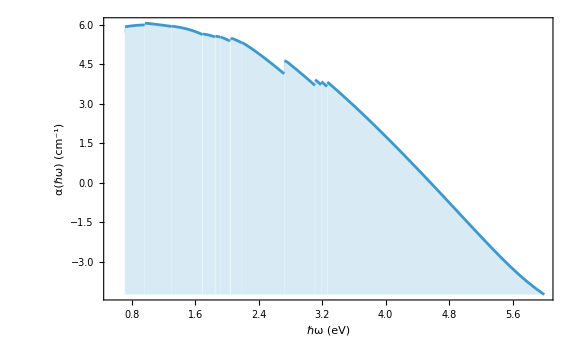

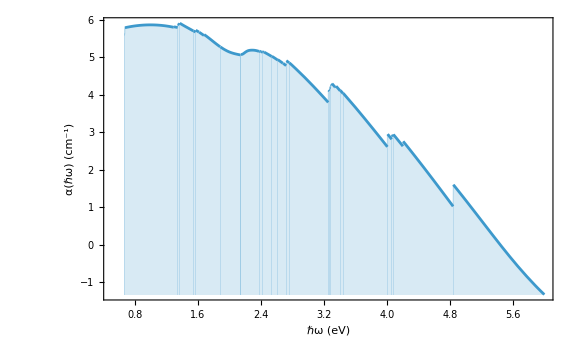

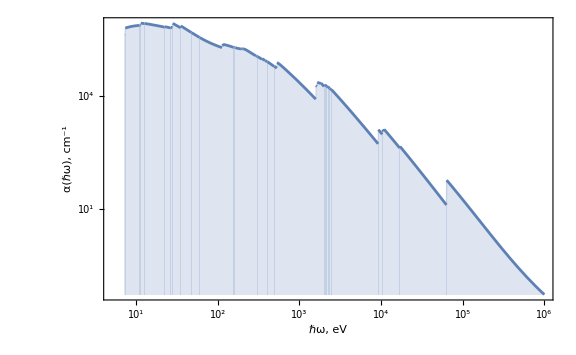

```mathematica
Plot[TotalAbsorption[x*10^-6],{x,Eg,10^6},PlotRange->{{0.7 Eg,10^6},Full},Frame->True,FrameLabel->{{Style["α(ℏω) (cm^-1)",20,Black],""},{Style["ℏω (eV)",20,Black],Style[compoundName,20,Black] }},ImageSize->Large,LabelStyle->Directive[FontSize->18,FontFamily->"Times",Black],GridLines->None,Filling->Bottom,ScalingFunctions->{"Log10","Log10"}]
```

```mathematica
S1=Table[0,{ii,Length[AtomsCross]}];Do[Do[If[AtomsCross⟦ii⟧⟦jj⟧⟦1⟧≠AtomsCross⟦ii⟧⟦jj+1⟧⟦1⟧,S1⟦ii⟧ +=0.9107 10^-2(AtomsCross⟦ii⟧⟦jj+1⟧⟦2⟧+AtomsCross⟦ii⟧⟦jj⟧⟦2⟧)(AtomsCross⟦ii⟧⟦jj+1⟧⟦1⟧-AtomsCross⟦ii⟧⟦jj⟧⟦1⟧)/2],{jj,Length[AtomsCross⟦ii⟧]-1}],{ii,Length[AtomsCross]}];S1
```

{10.0165,10.5979,11.6191,7.28647}

```mathematica
nn=2^15;eKraKroMax=10^-3;
KramersKronig[f_,emax_,nmax_]:=Block[{a},a=Table[f[(i-1)/nmax emax],{i,nmax}];a=Join[a,-Reverse[a]];a=Fourier[a];Do[a[[i]]=-a[[i]],{i,nmax,2 nmax}];Return[Im[InverseFourier[a]]]];
```

```mathematica
Clear[a];
a=KramersKronig[TotalEps2,eKraKroMax,nn];
reepsloc=Interpolation[Table[{N[(i-1)/nn eKraKroMax] 10^6,a⟦i⟧+1},{i,nn}],InterpolationOrder->1];
reeps[x_]:=If[x>N[(nn-1)/nn eKraKroMax] 10^6,1,reepsloc[x]];
```

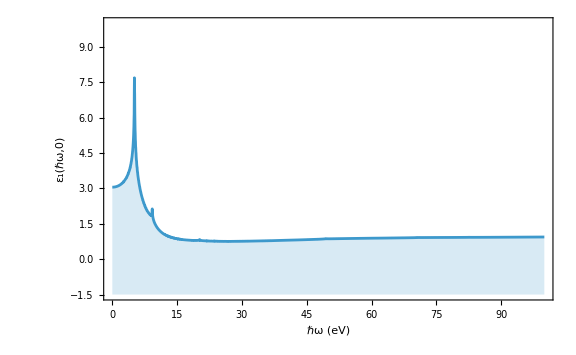

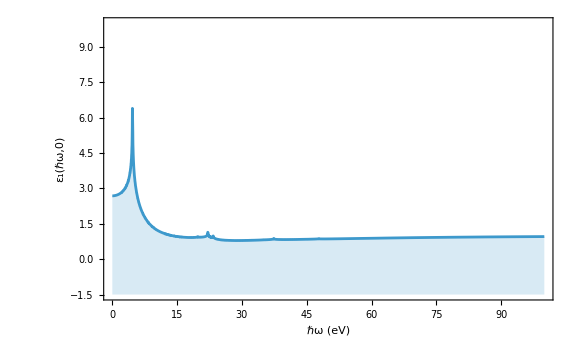

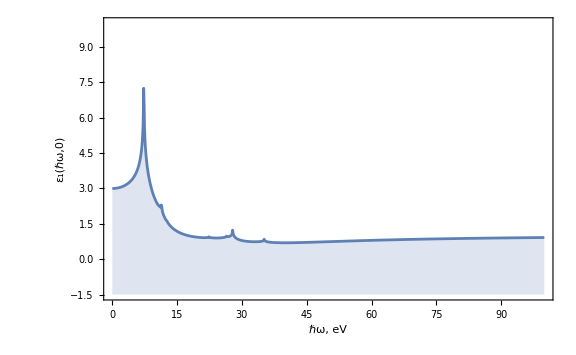

```mathematica
Plot[reeps[x],{x,0,100},PlotRange->{Full,{-1.5,10}},Frame->True,FrameLabel->{{Style["ε_1(ℏω,0)",20,Black],""},{Style["ℏω (eV)",20,Black],Style[compoundName,20,Black] }},ImageSize->Large,LabelStyle->Directive[FontSize->18,FontFamily->"Times",Black],GridLines->None,Filling->Bottom]
```

```mathematica
imepsinvlist=Join[Table[{N[(i-1)/nn eKraKroMax] 10^6,Im[-1/(a⟦i⟧+1 + ⅈ TotalEps2[(i-1)/nn eKraKroMax])]},{i,nn}],Table[{x,TotalEps2[x 10^-6]},{x,eKraKroMax 10^6+1,10000,1}],Table[{x,TotalEps2[x 10^-6]},{x,10010,100000,10}],Table[{x,TotalEps2[x 10^-6]},{x,100100,1000000,100}]];
imepsinv=Interpolation[imepsinvlist,InterpolationOrder->1];
```

```mathematica
Export[NotebookDirectory[]<>compoundName<>"_ImInvEps.txt",imepsinvlist,"Table"];
```

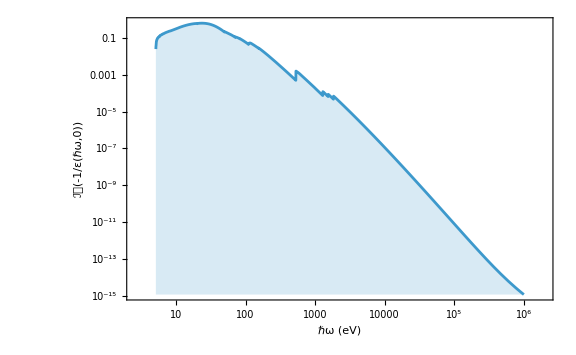

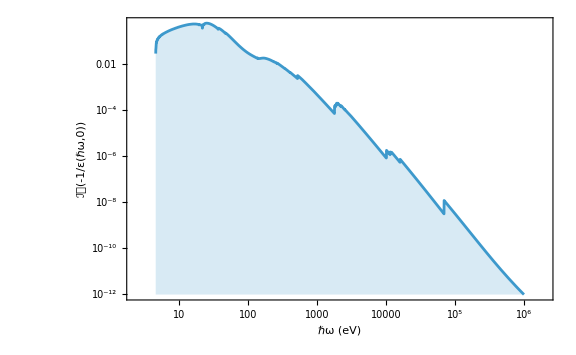

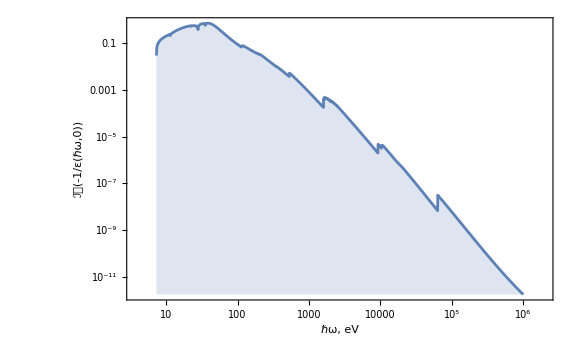

```mathematica
LogLogPlot[imepsinv[x],{x,Eg,10^6},PlotRange->{{0.5*Eg,2*10^6},Full},Frame->True,FrameLabel->{{Style["ℐ𝓂(-1/ε(ℏω,0))",20,Black],""},{Style["ℏω (eV)",20,Black],Style[compoundName ,20,Black]}},ImageSize->Large,LabelStyle->Directive[FontSize->18,FontFamily->"Times",Black],GridLines->None,Filling->Bottom]
```

```mathematica
Clear[refindex];
refindex[x_]:=If[x>N[(nn-1)/nn eKraKroMax] 10^6,1,√((reeps[x]+√((reeps[x])^2+(totEps2func[x])^2))/2)];
```

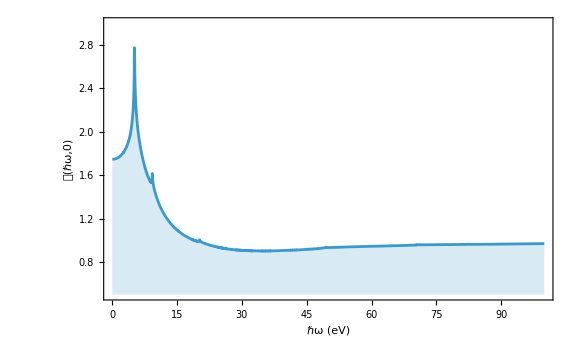

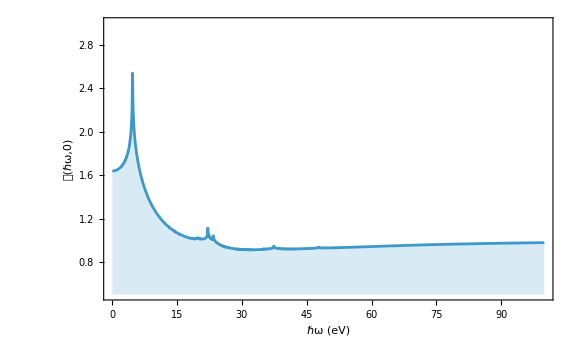

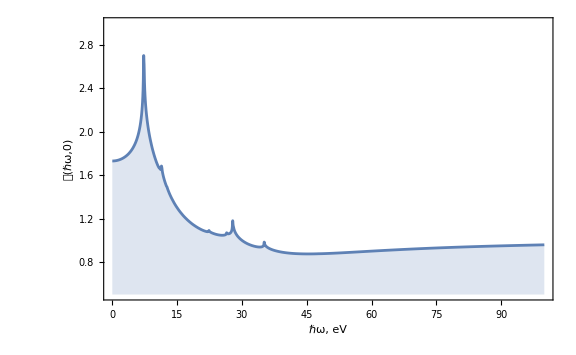

```mathematica
Plot[refindex[x],{x,0,100},PlotRange->{Full,{0.5,3.0}},Frame->True,FrameLabel->{{Style["𝓃(ℏω,0)",20,Black],""},{Style["ℏω (eV)",20,Black],Style[compoundName,20,Black] }},ImageSize->Large,LabelStyle->Directive[FontSize->18,FontFamily->"Times",Black],GridLines->None,Filling->Bottom]
```

```mathematica
partEps2ext[ω_,Εq_]:=If[Εq>0,Table[Εi=10^6(SubShells⟦ii⟧⟦7⟧-EnergyCorrections⟦SubShells⟦ii⟧⟦6⟧⟧);If[ω>Εi,
1/(4 √(Εq+10^-15) (ω+10^-15))*NIntegrate[x/(√(x-Εi)) partialEps2listfunc[[ii]][If[x>=10^6,10^6,x]],{x,Εi+(√(ω-Εi)-√Εq)^2,Εi+(√(ω-Εi)+√Εq)^2},Method->"LocalAdaptive"],0],{ii,Length[SubShells]}],Table[partialEps2listfunc[[ii]][ω],{ii,Length[SubShells]}]];
```

```mathematica
partEps2ext[10000,100000]//AbsoluteTiming
```

{0.239676,{0,0,0,1.17084×10^-10,3.77693×10^-10,1.54975×10^-10,1.89785×10^-10,1.44678×10^-11,1.6629×10^-11,1.21084×10^-10,4.89191×10^-11,5.83603×10^-11,4.61237×10^-12,5.2386×10^-12,4.10527×10^-14,4.59658×10^-14,2.1378×10^-11,7.09104×10^-12,7.98399×10^-12,0.,0.,0.,0,4.85353×10^-11,4.74183×10^-12,7.2673×10^-12,1.13128×10^-11,1.18619×10^-12,1.8172×10^-12,2.51171×10^-14,3.22545×10^-14,1.84262×10^-12,1.62978×10^-13,2.48163×10^-13,0.,0.,0.,1.81706×10^-11,1.75039×10^-12,1.65613×10^-14,2.96696×10^-14,1.5262×10^-13,7.97862×10^-17,1.39584×10^-16,8.66362×10^-12,5.39393×10^-13,1.07328×10^-15,1.9756×10^-15}}

```mathematica
listΕq={0,3,6,10,30,60,100,300,600,1000,3000,6000,10000,30000,60000,100000,300000,600000,1000000};
listω=Join[Table[ω,{ω,0,100,0.1}],Table[ω,{ω,101,1000,1}],Table[ω,{ω,1010,10000,10}],Table[ω,{ω,10100,100000,100}],Table[ω,{ω,101000,1000000,1000}]];
partEps2extlist=Flatten[ParallelTable[Join[{listω[[ii]],listΕq[[jj]]},partEps2ext[listω[[ii]],listΕq[[jj]]]],{ii,Length[listω]},{jj,Length[listΕq]}],1];
partEps2extfunc=ParallelTable[Interpolation[partEps2extlist[[All,{1,2,ii}]],InterpolationOrder->1],{ii,3,Length[partEps2extlist[[1]]]}];
```

```mathematica
Export[NotebookDirectory[]<>compoundName<>"_PatialEps2ext.txt",partEps2extlist,"Table"];
```

```mathematica
iminvepsextlist=Flatten[ParallelTable[{listω[[kk]],listΕq[[jj]],Im[-(reeps[listω[[kk]]]+I Sum[partEps2extfunc[[ii]][listω[[kk]],listΕq[[jj]]],{ii,Length[SubShells]}])^-1]},{kk,Length[listω]},{jj,Length[listΕq]}],1];
iminvepsext=Interpolation[iminvepsextlist,InterpolationOrder->1];
```

```mathematica
Export[NotebookDirectory[]<>compoundName<>"_ImInvEpsext.txt",iminvepsextlist,"Table"];
```

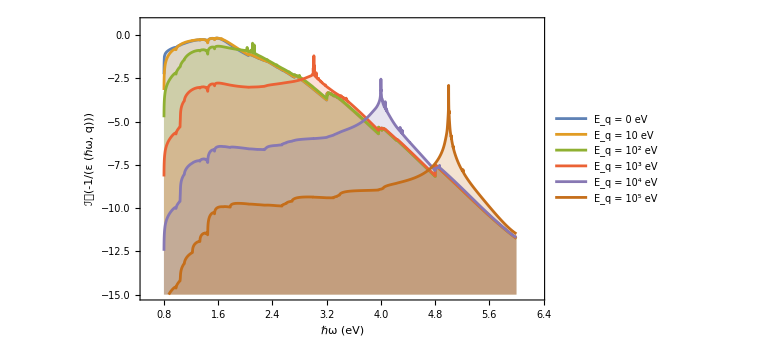

```mathematica
ListLinePlot[{Table[{10^x,iminvepsext[10^x,0]},{x,0,6,0.001}],Table[{10^x,iminvepsext[10^x,10]},{x,0,6,0.001}],Table[{10^x,iminvepsext[10^x,100]},{x,0,6,0.001}],Table[{10^x,iminvepsext[10^x,1000]},{x,0,6,0.001}],Table[{10^x,iminvepsext[10^x,10000]},{x,0,6,0.001}],Table[{10^x,iminvepsext[10^x,100000]},{x,0,6,0.001}]},PlotRange->{{0.5*Eg,2 10^6},{10^-15,5}},ScalingFunctions->{"Log10","Log10"},Frame->True,FrameLabel->{{Style["ℐ𝓂(-1/(ε (ℏω, q)))",20,Black],""},{Style["ℏω (eV)",20,Black],Style[compoundName ,20,Black]}},ImageSize->Large,LabelStyle->Directive[FontSize->18,FontFamily->"Times",Black],GridLines->None,Filling->Bottom,PlotLegends->{"Ε_q = 0 eV","Ε_q = 10 eV","Ε_q = 10^2 eV","Ε_q = 10^3 eV","Ε_q = 10^4 eV","Ε_q = 10^5 eV"}]
```

```mathematica
imepsinvlist=Import["/home/yauhenitalochka/mnt/Files/Condensed matter physics/Dissertation/L(Y)SO/Lu1.6Y0.4SiO5/LYSO_ImInvEps.txt","Table"];
imepsinv=Interpolation[imepsinvlist,InterpolationOrder->1];
partEps2list=Import["/home/yauhenitalochka/mnt/Files/Condensed matter physics/Dissertation/L(Y)SO/Lu1.6Y0.4SiO5/LYSO_PatialEps2.txt","Table"];
dimpE2=Dimensions[partEps2list,2];
totEps2func=Interpolation[Table[{partEps2list⟦i,1⟧,Sum[partEps2list⟦i,j⟧,{j,2,dimpE2⟦2⟧}]},{i,dimpE2⟦1⟧}],InterpolationOrder->1];
partialEps2listfunc=Table[Interpolation[Table[{partEps2list⟦i,1⟧,partEps2list⟦i,j⟧},{i,dimpE2⟦1⟧}],InterpolationOrder->1],{j,2,dimpE2⟦2⟧}];
TotalEps2[x_]:=totEps2func[x*10^6];
```

```mathematica
partEps2extlist=Import["/home/yauhenitalochka/mnt/Files/Condensed matter physics/Dissertation/L(Y)SO/Lu1.6Y0.4SiO5/LYSO_PatialEps2ext.txt","Table"];
partEps2extfunc=Table[Interpolation[partEps2extlist[[All,{1,2,ii}]],InterpolationOrder->1],{ii,3,Length[partEps2extlist[[1]]]}];
totEps2extfunc=Interpolation[Table[{partEps2extlist⟦i,1⟧,partEps2extlist⟦i,2⟧,Sum[partEps2extlist[[i,j]],{j,3,Length[partEps2extlist[[1]]]}]},{i,Length[partEps2extlist]}],InterpolationOrder->1];
iminvepsextlist=Import["/home/yauhenitalochka/mnt/Files/Condensed matter physics/Dissertation/L(Y)SO/Lu1.6Y0.4SiO5/LYSO_ImInvEpsext.txt","Table"];
iminvepsext=Interpolation[iminvepsextlist,InterpolationOrder->1];
```

```mathematica
mc2=510998.95;
Ζ=-1;
aB=0.05291772085936;
mec2=510998.95;
ℱq[en_,ω_,iminveps_]:=If[en>ω,NIntegrate[(x+mec2)/((x+10^-15) (x+2 mec2))iminveps[ω,If[x>=10^5,10^5,x]],{x,√((√en√(en+2 mc2)-√(en-ω)√(en-ω+2 mc2))^2+(mec2)^2)-mec2,√((√en√(en+2 mc2)+√(en-ω)√(en-ω+2 mc2))^2+(mec2)^2)-mec2},Method->"LocalAdaptive"],0];
dedx[en_,ℱ_]:=Ζ^2/(π aB) NIntegrate[ω/en (2 mc2)/mec2 (1+en/mc2)^2/(2+en/mc2) ℱ[en,ω],{ω,0,en},Method->"LocalAdaptive"];
λinvtot[en_,ℱ_]:=Ζ^2/(π aB) NIntegrate[1/en (2 mc2)/mec2 (1+en/mc2)^2/(2+en/mc2) ℱ[en,ω],{ω,0,en},Method->"LocalAdaptive"];
λinvpart[en_,ℱ_,parteps2_,toteps2_]:=Ζ^2/(π aB) NIntegrate[1/en (2 mc2)/mec2 (1+en/mc2)^2/(2+en/mc2) ℱ[en,ω] parteps2[ω]/(toteps2[ω]+10^-20),{ω,0,en},Method->"LocalAdaptive"];
```

```mathematica
listω=Join[Table[ω,{ω,0,10,0.1}],Table[ω,{ω,11,1000,1}],Table[ω,{ω,1010,10000,10}],Table[ω,{ω,10100,100000,100}],Table[ω,{ω,101000,1000000,1000}]];
ℱqlist=Flatten[ParallelTable[{10^x,listω[[jj]],ℱq[10^x,listω[[jj]],iminvepsext]},{x,0,6,0.02},{jj,Length[listω]}],1];
ℱqfunc=Interpolation[ℱqlist,InterpolationOrder->1];
```

```mathematica
Export[NotebookDirectory[]<>compoundName<>"_Fqlist.txt",ℱqlist,"Table"];
```

```mathematica
ℱq[100,10,iminvepsext]//AbsoluteTiming
```

{0.668802,0.551982}

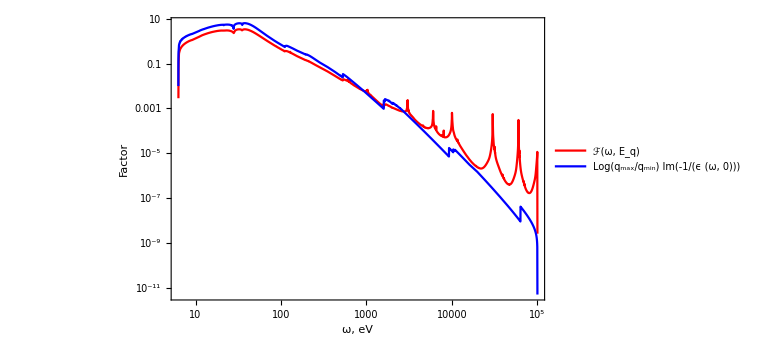

```mathematica
Plot[Evaluate[{ℱqfunc[en,ω], Log[(√en √(en+2 mc2)+√(en-ω)√(en-ω+2 mc2))/(√en √(en+2 mc2)-√(en-ω)√(en-ω+2 mc2))]imepsinv[ω]}/.{en->10^5}],{ω,5,10^5},PlotRange->All,ScalingFunctions->{"Log10","Log10"},PlotStyle->{{Red,Thick},{Blue,Thick}},PlotLegends->{"ℱ(ω, E_q)","Log(q_max/q_min) Im(-1/(ϵ (ω, 0)))"},PlotTheme->"Scientific",FrameStyle->Directive[Thickness[0.003],Black],FrameLabel->{Style["ℏω (eV)",20,Black],Style["Factor ",20,Black]},ImageSize->Large,LabelStyle->Directive[FontSize->18,FontFamily->"Times"]]
```

```mathematica
ℱqlist=Import["D:\\Files\\Condensed matter physics\\Dissertation\\L(Y)SO\\Lu1.6Y0.4SiO5\\LYSO_Fqlist_e.txt","Table"];
ℱqfunc=Interpolation[ℱqlist,InterpolationOrder->1];
```

```mathematica
mc2=510998.95;
Ζ=-1;
aB=0.05291772085936;
mec2=510998.95;
dedx[en_,iminveps_]:=Ζ^2/(π aB) NIntegrate[ω/en (2 mc2)/mec2 (1+en/mc2)^2/(2+en/mc2) Log[(√en √(en+2 mc2)+√(en-ω)√(en-ω+2 mc2))/(√en √(en+2 mc2)-√(en-ω)√(en-ω+2 mc2))]iminveps[ω],{ω,0,en},Method->"LocalAdaptive"];
λinvtot[en_,iminveps_]:=Ζ^2/(π aB) NIntegrate[1/en (2 mc2)/mec2 (1+en/mc2)^2/(2+en/mc2) Log[(√en √(en+2 mc2)+√(en-ω)√(en-ω+2 mc2))/(√en √(en+2 mc2)-√(en-ω)√(en-ω+2 mc2))]iminveps[ω],{ω,0,en},Method->"LocalAdaptive"];
λinvpart[en_,iminveps_,parteps2_,toteps2_]:=Ζ^2/(π aB) NIntegrate[1/en (2 mc2)/mec2 (1+en/mc2)^2/(2+en/mc2) Log[(√en √(en+2 mc2)+√(en-ω)√(en-ω+2 mc2))/(√en √(en+2 mc2)-√(en-ω)√(en-ω+2 mc2))]iminveps[ω]parteps2[ω]/(toteps2[ω]+10^-10),{ω,0,en},Method->"LocalAdaptive"];
```

```mathematica
Quiet[dedxtab=ParallelTable[{10^x,dedx[10^x,imepsinv]},{x,0,6,0.01}];]
```

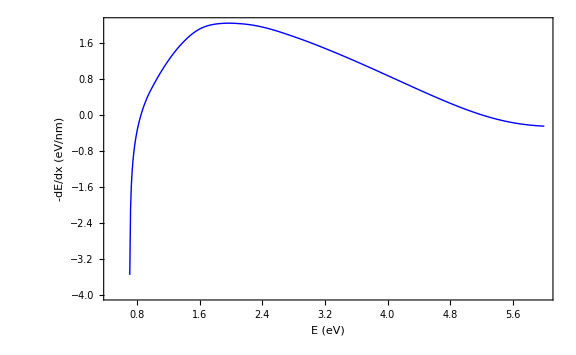

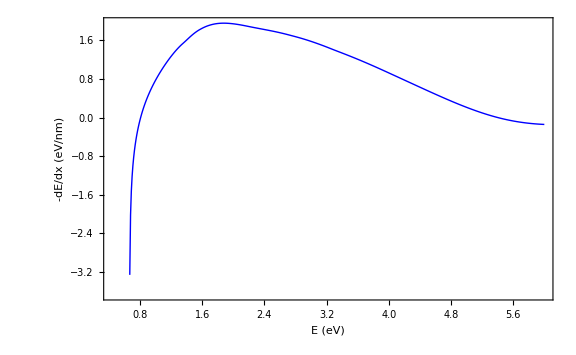

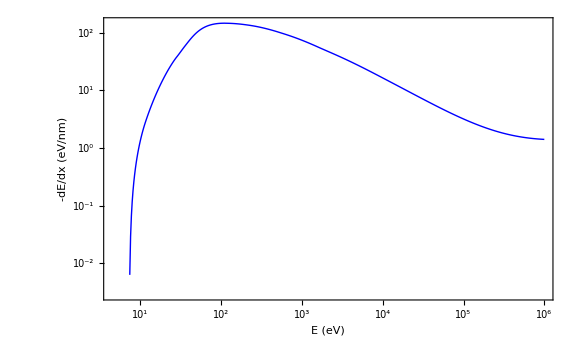

```mathematica
ListPlot[dedxtab,PlotRange->All,Joined->True,PlotStyle->{Thick,Blue},ImageSize->Large,Frame->True,FrameLabel->{{Style["-dE/dx (eV/nm)",20,Black],""},{Style["E (eV)",20,Black],Style[compoundName,20,Black]}},ImageSize->Large,LabelStyle->Directive[FontSize->18,FontFamily->"Times",Black],GridLines->None,ScalingFunctions->{"Log10","Log10"}]
```

```mathematica
Table[{i,SubShells[[All,1]][[i]],Round[Abs[SubShells⟦i⟧⟦5⟧+PopulationCorrections⟦i⟧⟦2⟧],0.1],N[Round[SubShells[[All,7]][[i]]-EnergyCorrections[[SubShells[[All,6]][[i]]]]-Eg*10^-6,10^-9]/10^-6]},{i,1,Length[SubShells]}]
```

{{1,Mg1s1/2,6.,1282.49},{2,Mg2s1/2,6.,77.45},{3,Mg2p1/2,6.,44.54},{4,Mg2p3/2,12.,44.23},{5,Mg3s1/2,0.,-5.12},{6,Al1s1/2,4.,1534.62},{7,Al2s1/2,4.,103.77},{8,Al2p1/2,4.,65.92},{9,Al2p3/2,8.,65.45},{10,Al3s1/2,0.,-5.12},{11,Al3p1/2,0.,-10.4},{12,Al3p3/2,0.,-10.41},{13,Si1s1/2,6.,1826.08},{14,Si2s1/2,6.,149.13},{15,Si2p1/2,6.,106.25},{16,Si2p3/2,12.,105.56},{17,Si3s1/2,0.,11.21},{18,Si3p1/2,0.5,4.13},{19,Si3p3/2,1.,4.1},{20,O1s1/2,24.,523.13},{21,O2s1/2,24.,15.08},{22,O2p1/2,23.5,0.04},{23,O2p3/2,47.,0.}}

```mathematica
Groups={{"Mg1s"},{"Mg2s","Mg2p"},{"Al1s"},{"Al2s","Al2p"},{"Si1s"},{"Si2s","Si2p"},{"Si3p"},{"O1s"},{"O2s"},{"O2p"}};
```

```mathematica
GroupIndeces=Table[Select[Table[{i,SubShells[[All,1]][[i]]},{i,Length[SubShells]}],StringStartsQ[#[[2]],Groups[[i]]]&][[All,1]],{i,Length[Groups]}]
```

{{1},{2,3,4},{6},{7,8,9},{13},{14,15,16},{18,19},{20},{21},{22,23}}

```mathematica
SetSystemOptions["CheckMachineUnderflow"->False];
λinvlist=Join[ParallelTable[{10^x,Quiet[Clear[locf];locf[en_]=#;λinvpart[10^x,imepsinv,locf,totEps2func]]},{x,0,6,0.01}]&/@(Sum[partialEps2listfunc⟦j⟧[en],{j,#}]&/@GroupIndeces),{ParallelTable[{10^x,Quiet[λinvtot[10^x,imepsinv]]},{x,0,6,0.01}]}];
```

```mathematica
λlist=Table[λ=λinvlist[[i]];
λ[[All,2]]=1/(λ[[All,2]]+10^-9);λ,{i,Length[λinvlist]}];
Clear[λ];
```

```mathematica
namelist={"Mg1s","Mg2ps","Al1s","Al2ps","Si1s","Si2ps","Si3p","O1s","O2s","O2p","total"};
```

```mathematica
Do[kk=1;
Do[If[kk>(Length[λlist[[j]]]-1),Break[];];If[λlist[[j]][[kk+1,2]]>=10^9,λlist[[j]]=Delete[λlist[[j]],kk];--kk;];kk++;,{i,1,Length[λlist[[j]]]-1}],{j,1,Length[λlist]}]
```

```mathematica
λlist=Table[Import[NotebookDirectory[]<>"imfp_e/"<>namelist[[i]]<>"_IMFP.txt","Table"],{i,14}];
```

```mathematica
Do[Export[NotebookDirectory[]<>"imfp_e/"<>namelist[[i]]<>"_IMFP.txt",λlist[[i]],"Table"],{i,Length[λlist]}]
```

```mathematica
yticks={{10^-2,"10^-2"},{10^-1,"10^-1"},{10^0,"10^0"},{10^1,"10^1"},{10^2,"10^2"},{10^3,"10^3"},{10^4,"10^4"},{10^5,"10^5"},{10^6,"10^6"},{10^7,"10^7"},{10^8,"10^8"},{10^9,"10^9"}};
xticks={{10^0,"10^0"},{10^1,"10^1"},{10^2,"10^2"},{10^3,"10^3"},{10^4,"10^4"},{10^5,"10^5"},{10^6,"10^6"}};
```

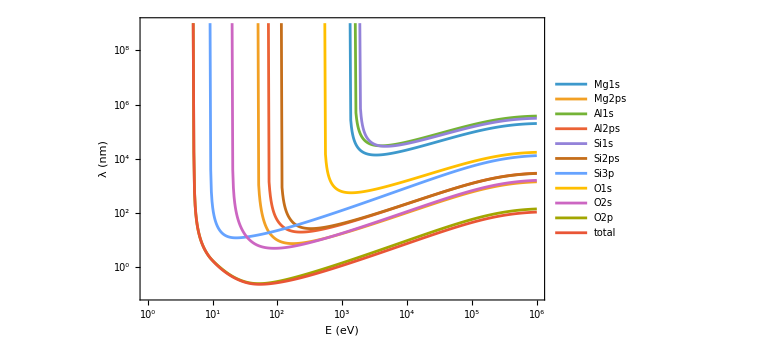

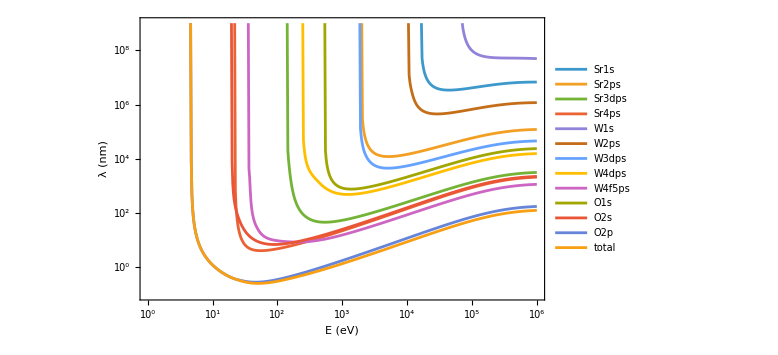

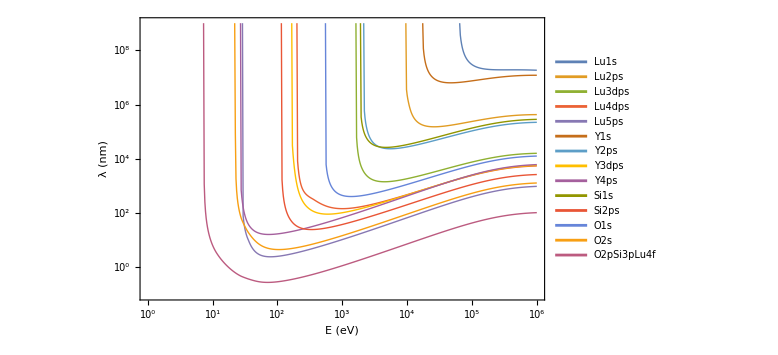

```mathematica
ListPlot[λlist,PlotRange->{{1,10^6},{0.1,10^9}},Joined->True,PlotStyle->Thick,ImageSize->Large,Frame->True,FrameLabel->{{Style["λ (nm)",20,Black],""},{Style["E (eV)",20,Black],Style[compoundName,20,Black]}},ImageSize->Large,LabelStyle->Directive[FontSize->18,FontFamily->"Times",Black],GridLines->None,ScalingFunctions->{"Log10","Log10"},PlotLegends->namelist,FrameTicks->{{yticks,None},{xticks,None}}]
```